```mathematica
(* First 21-digit prime in the digits of ⅇ: *)
(* Estimation: *)
PrimePi[10^21]
```

21127269486018731928

```mathematica
N[RiemannR[10^21]-RiemannR[10^20],13]
```

1.890644988338×10^19

```mathematica
(* From https://en.wikipedia.org/wiki/Prime-counting_function: *)
21127269486018731928-2220819602560918840
```

18906449883457813088

```mathematica
𝒫rob=(RiemannR[10^21]-RiemannR[10^20])/(10^21-10^20)//N
```

0.0210072

```mathematica
1/𝒫rob
```

47.6028

```mathematica
primeDelta=DeleteDuplicatesBy[Last]@Table[{i, PrimeQ[FromDigits[Take[RealDigits[ⅇ,10, 21+2 Ceiling[1/𝒫rob]][[1]], {1+i,1+i+20}]]]}, {i, 1, 2 Ceiling[1/𝒫rob]}]
```

{{1,False},{51,True}}

```mathematica
i=primeDelta[[2]][[1]]
```

51

```mathematica
𝒫1st=FromDigits[Take[RealDigits[ⅇ,10, 21 +2 Ceiling[1/𝒫rob]][[1]], {1+i,1+i+20}]]
```

957496696762772407663

```mathematica
N[ⅇ, 21+i]
```

2.71828182845904523536028747135266249775724709369995957496696762772407663

```mathematica
RealDigits[ⅇ, 10, 21, -i][[1]]
```

{9,5,7,4,9,6,6,9,6,7,6,2,7,7,2,4,0,7,6,6,3}

```mathematica
PrimeQ[𝒫1st]
```

True

```mathematica
(* n-digit primes in ⅇ: *)
𝒫rob=.
𝒫rob[n_]:=(RiemannR[10^n]-RiemannR[10^(n-1)])/(10^n-10^(n-1))//N
```

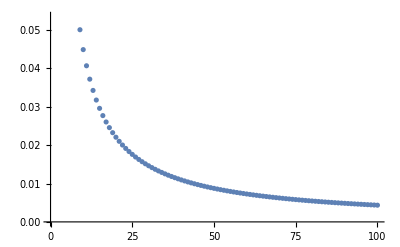

```mathematica
(* PLot of the probability of a n-digit number being prime: *)
ListPlot[Table[𝒫rob[n], {n, 1, 100}]]
```

```mathematica
(* Positions of the first n-digit primes in ⅇ: *)
ℒ=Table[FirstCase[Table[{i,PrimeQ[FromDigits[Take[RealDigits[ⅇ,10, n+5 Ceiling[1/𝒫rob[n]]][[1]], {i,i+n-1}]]]∧Take[RealDigits[ⅇ,10, n+5 Ceiling[1/𝒫rob[n]]][[1]], {i,i}]≠ {0} }, {i, 1, 5 Ceiling[1/𝒫rob[n]]}], {x_, True}-> x-1], {n, 1, 21}]
```

{0,1,0,14,24,12,0,64,19,99,37,53,7,47,39,40,8,82,151,18,51}

```mathematica
(* First n-digit primes in ⅇ: *)
(* {digits, offset, prime} *)
Table[{n,ℒ[[n]],FromDigits[Take[RealDigits[ⅇ,10, n+5 Ceiling[1/𝒫rob[n]]][[1]], {ℒ[[n]]+1,ℒ[[n]]+n}]]}, {n, 1, 21}]
```

{{1,0,2},{2,1,71},{3,0,271},{4,14,4523},{5,24,74713},{6,12,904523},{7,0,2718281},{8,64,72407663},{9,19,360287471},{10,99,7427466391},{11,37,75724709369},{12,53,749669676277},{13,7,8284590452353},{14,47,99959574966967},{15,39,724709369995957},{16,40,2470936999595749},{17,8,28459045235360287},{18,82,571382178525166427},{19,151,5956307381323286279},{20,18,53602874713526624977},{21,51,957496696762772407663}}

```mathematica
N[ⅇ, 21]
```

2.71828182845904523536

```mathematica
(* Positions of the first n-digit primes in π: *)
ℒ=Table[FirstCase[Table[{i,PrimeQ[FromDigits[Take[RealDigits[π,10, n+5 Ceiling[1/𝒫rob[n]]][[1]], {i,i+n-1}]]]∧Take[RealDigits[ⅇ,10, n+5 Ceiling[1/𝒫rob[n]]][[1]], {i,i}]≠ {0} }, {i, 1, 5 Ceiling[1/𝒫rob[n]]}], {x_, True}-> x-1], {n, 1, 21}]
```

{0,0,7,2,1,0,3,33,29,4,14,1,5,16,35,81,11,86,25,11,24}

```mathematica
(* First n-digit primes in π: *)
(* {digits, offset, prime} *)
Table[{n,ℒ[[n]],FromDigits[Take[RealDigits[π,10, n+5 Ceiling[1/𝒫rob[n]]][[1]], {ℒ[[n]]+1,ℒ[[n]]+n}]]}, {n, 1, 21}]
```

{{1,0,3},{2,0,31},{3,7,653},{4,2,4159},{5,1,14159},{6,0,314159},{7,3,1592653},{8,33,28841971},{9,29,795028841},{10,4,5926535897},{11,14,93238462643},{12,1,141592653589},{13,5,9265358979323},{14,16,23846264338327},{15,35,841971693993751},{16,81,8628034825342117},{17,11,89793238462643383},{18,86,348253421170679821},{19,25,3832795028841971693},{20,11,89793238462643383279},{21,24,338327950288419716939}}

```mathematica
N[π, 24+21+1]
```

3.141592653589793238462643383279502884197169399

```mathematica
Table[{i,RiemannR[10^i]-RiemannR[10^(i-1)]//N}, {i, 21, 30}]
```

{{21,1.89064×10^19},{22,1.8034×10^20},{23,1.72385×10^21},{24,1.65103×10^22},{25,1.58411×10^23},{26,1.5224×10^24},{27,1.46532×10^25},{28,1.41237×10^26},{29,1.36311×10^27},{30,1.31717×10^28}}